```mathematica
(* This is to get the SSM potential between Ca and Cl*)
```

```mathematica
(* The main task is to get v_{R1,Ca Water} , v_{R1, Cl Water} and  v_{R1,Ca Cl}. I will denote it by fvR1CaA, fvR1ClA and fvR1CaCl respectively *)
```

```mathematica
(* This handling of the surface charge is a bit tricky. Maybe use a smoothed charge will make the analysis easier. I can just use the delta charge for now *)
(* when a surface charge of Q is convoluted with a potention ϕ. The 
 result is NIntegrate[Q/2 ϕ[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}], where rqcut is the position of the surface charge *)
```

```mathematica
(* The screening charge around ion Ca is denoted by frhoqCa for the full system and frhoqCa0 for the GT system. Definition is similar for the Cl *)
```

```mathematica
Quit[]
```

```mathematica
ϵ=71
```

71

```mathematica
Qca=2
Qcashield=-Qca (1 -1/ϵ)
```

2

-140/71

```mathematica
Qcl=-1
Qclshield=-Qcl(1 -1/ϵ)
```

-1

70/71

```mathematica
d=0.2
ss=6
fintqcorrect[r_]:=Piecewise[{{0, r<d}, {Erf[(r-d)/ss], r≥d}}]
frhoqcorrect[r_]:=Piecewise[{{0, r<d}, {fintqcorrect'[r]/(4π r^2), r≥d}}]
```

0.2

6

```mathematica
frhoqcorrect2[r_]:=Piecewise[{{0, r<d}, {(Erf'[(r-d)/ss]/ss)/(4π r^2), r≥d}}]
```

```mathematica
frhoqcorrect[0.21]
```

0.339355

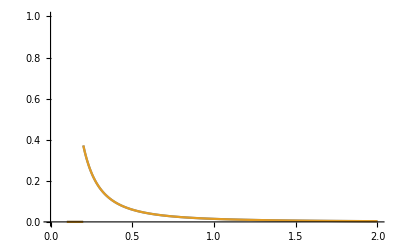

```mathematica
Plot[{frhoqcorrect[r],frhoqcorrect2[r]},{r,0.1,2},PlotRange->{0,1}]
```

```mathematica
NIntegrate[frhoqcorrect2[r]4π r^2,{r,0,100}]
```

1.

```mathematica
(* frhoqCa0=frhoqCa-Qcashield frhoqcorrect, without considering the surface charge, total surface charge is Qcashield-Qcacut *)
```

```mathematica
rrhoqCa=Import["rhoq_Ca_full.txt","Table"];
```

```mathematica
frhoqCa=Interpolation[rrhoqCa]
```

InterpolatingFunction[…]

```mathematica
rrhoqCl=Import["rhoq_Cl_full.txt","Table"];
```

```mathematica
frhoqCl=Interpolation[rrhoqCl]
```

InterpolatingFunction[…]

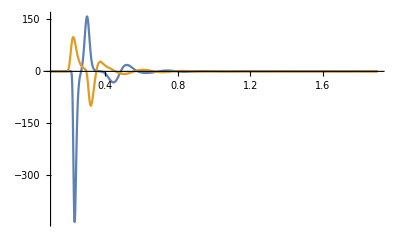

```mathematica
Plot[{frhoqCa[r],frhoqCl[r]},{r,0.1,1.9},PlotRange->Full]
```

```mathematica
frhoqCa0[r_]:=frhoqCa[r]-Qcashield frhoqcorrect[r]
```

```mathematica
frhoqCl0[r_]:=frhoqCl[r]-Qclshield frhoqcorrect[r]
```

```mathematica
rqcut=1.92
```

1.92

```mathematica
Qcacut=NIntegrate[frhoqCa[rp] 4 π rp^2,{rp,0,rqcut}]
```

-1.95456

```mathematica
Qcacut-Qcashield
```

0.0172741

```mathematica
Qclcut=NIntegrate[frhoqCl[rp] 4 π rp^2,{rp,0,rqcut}]
```

0.97812

```mathematica
Qclcut-Qclshield
```

-0.00779583

```mathematica
fG[r_,rp_,s_]:=1/(2 r rp)(Abs[r+rp] Erf[Abs[r+rp]/s] + s/Sqrt[π] Exp[-(Abs[r+rp]/s)^2] 
            - Abs[r-rp]Erf[Abs[r-rp]/s] - s/Sqrt[π] Exp[-(Abs[r-rp]/s)^2] )
```

```mathematica
rhosurf[r_,rcut_]:=DiracDelta[r-rcut]/(4 π rcut^2)
```

```mathematica
fVR1surf[r_,rcut_]:=1/(2 r rcut)(-0.28209479177387814 ⅇ^(-4. Abs[r-rcut]^2)+0.28209479177387814 ⅇ^(-4. Abs[r+rcut]^2)-Abs[r-rcut] Erf[2. Abs[r-rcut]]+Abs[r+rcut] Erf[2. Abs[r+rcut]])
```

```mathematica
(* to get fVR1surf, we already assumed that the smoothed length sigma=0.5 *)
```

```mathematica
(* Calculate fVR1CaA first *)
```

```mathematica
s=0.5 (* the sigma parameter for v1 *)
```

0.5

```mathematica
frenormCaA[r_?NumericQ]:=NIntegrate[frhoqCa[rp]fG[r,rp,s]4π rp^2,{rp,0.01,rqcut}]+(Qcashield-Qcacut) fVR1surf[r,rqcut]
```

```mathematica
tableVrenormCaA=ParallelTable[frenormCaA[r],{r,0.01,4.91,0.05}]
```

{-4.28972,-4.27124,-4.22696,-4.15832,-4.0675,-3.95727,-3.83086,-3.69174,-3.54345,-3.38944,-3.23291,-3.07672,-2.92329,-2.77458,-2.63208,-2.49684,-2.36951,-2.25038,-2.13949,-2.03665,-1.94151,-1.85361,-1.77246,-1.69753,-1.62827,-1.56418,-1.50477,-1.44961,-1.39829,-1.35044,-1.30573,-1.26388,-1.22463,-1.18774,-1.153,-1.12025,-1.0893,-1.06002,-1.03228,-1.00595,-0.980938,-0.957137,-0.934464,-0.912841,-0.892195,-0.872463,-0.853584,-0.835504,-0.818174,-0.801547,-0.785583,-0.770241,-0.755487,-0.741287,-0.727611,-0.71443,-0.701718,-0.689451,-0.677605,-0.666159,-0.655093,-0.644389,-0.634029,-0.623997,-0.614278,-0.604856,-0.595719,-0.586854,-0.57825,-0.569893,-0.561775,-0.553885,-0.546214,-0.538752,-0.531491,-0.524423,-0.517541,-0.510837,-0.504305,-0.497937,-0.491728,-0.485673,-0.479764,-0.473998,-0.468368,-0.462871,-0.457501,-0.452255,-0.447127,-0.442115,-0.437213,-0.432419,-0.427729,-0.42314,-0.418648,-0.41425,-0.409944,-0.405727,-0.401595}

```mathematica
interpVrenormCaA=Interpolation[Transpose[{Table[r,{r,0.01,4.91,0.05}],tableVrenormCaA}]]
```

InterpolatingFunction[…]

```mathematica
fVR1CaA[r_]:=Piecewise[{{interpVrenormCaA[r]+Qca Erf[r/s]/r, r<4.5}, {Qca/(ϵ r), r≥ 4.5}}]
```

```mathematica
fvR1CaA[r_]:=fVR1CaA[r]/Qca
```

InterpolatingFunction::dmval: Input value {0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

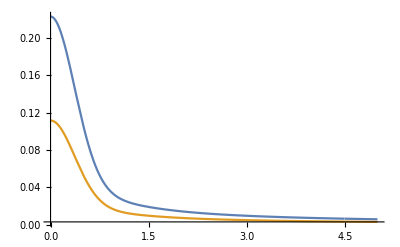

```mathematica
Plot[{fVR1CaA[r],fvR1CaA[r]},{r,0,5},PlotRange->Full]
```

```mathematica
(* successfully obtained fvR1CaA *)
```

```mathematica
fvR1CaA[0.5]
```

0.0532598

```mathematica
frenormClA[r_?NumericQ]:=NIntegrate[frhoqCl[rp]fG[r,rp,s]4π rp^2,{rp,0.01,rqcut}]+(Qclshield-Qclcut) fVR1surf[r,rqcut]
```

```mathematica
tableVrenormClA=ParallelTable[frenormClA[r],{r,0.01,4.91,0.05}]
```

{2.1647,2.15519,2.13242,2.09714,2.05049,1.99393,1.92914,1.85792,1.78212,1.70353,1.62379,1.54436,1.46647,1.39112,1.31905,1.25076,1.18657,1.1266,1.07086,1.01922,0.971488,0.927431,0.886779,0.849257,0.81459,0.782517,0.752794,0.725196,0.699518,0.675577,0.653209,0.632268,0.612623,0.594159,0.576774,0.560375,0.544882,0.530221,0.516327,0.503141,0.490612,0.478691,0.467336,0.456507,0.446168,0.436288,0.426837,0.417787,0.409114,0.400794,0.392806,0.385131,0.377751,0.370649,0.363809,0.357218,0.350861,0.344726,0.338803,0.33308,0.327547,0.322195,0.317015,0.311999,0.307139,0.302428,0.29786,0.293427,0.289125,0.284947,0.280888,0.276943,0.273107,0.269376,0.265745,0.262212,0.25877,0.255419,0.252152,0.248969,0.245864,0.242836,0.239882,0.236999,0.234184,0.231436,0.228751,0.226127,0.223564,0.221057,0.218607,0.21621,0.213865,0.21157,0.209324,0.207125,0.204972,0.202863,0.200797}

```mathematica
interpVrenormClA=Interpolation[Transpose[{Table[r,{r,0.01,4.91,0.05}],tableVrenormClA}]]
```

InterpolatingFunction[…]

```mathematica
fVR1ClA[r_]:=Piecewise[{{interpVrenormClA[r]+Qcl Erf[r/s]/r, r<4.5}, {Qcl/(ϵ r), r≥ 4.5}}]
```

```mathematica
fvR1ClA[r_]:=fVR1ClA[r]/Qcl
```

InterpolatingFunction::dmval: Input value {0.0000921329} lies outside the range of data in the interpolating function. Extrapolation will be used.

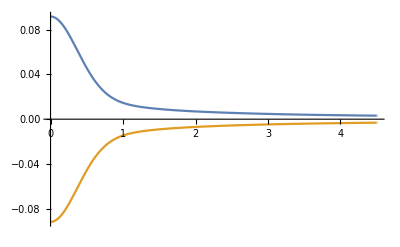

```mathematica
Plot[{fvR1ClA[r],fVR1ClA[r]},{r,0,4.51},PlotRange->Full]
```

```mathematica
frenormCaCl[r_?NumericQ]:=-1/Qca(NIntegrate[2 π rp^2 frhoqCa[rp] (fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]]-Erf[Sqrt[rp^2+r^2-2 r rp x]/s]/Sqrt[rp^2+r^2-2 r rp x]),{rp, 0.01, rqcut},{x,-1,1}]+ NIntegrate[(Qcashield-Qcacut)/2 (fvR1ClA[Sqrt[rqcut^2+r^2-2 r rqcut x]]-Erf[Sqrt[rqcut^2+r^2-2 r rqcut x]/s]/Sqrt[rqcut^2+r^2-2 r rqcut x]),{x,-1,1}])
```

```mathematica
tablerenormCaCl=ParallelTable[frenormCaCl[r],{r,0.005,3,0.05}]
```

{-2.062,-2.05477,-2.03571,-2.00542,-1.96481,-1.91506,-1.85758,-1.79388,-1.72553,-1.6541,-1.58104,-1.50769,-1.43519,-1.3645,-1.29637,-1.23136,-1.16983,-1.112,-1.05793,-1.00759,-0.960871,-0.917587,-0.877532,-0.840475,-0.806177,-0.774404,-0.744932,-0.717551,-0.692067,-0.668304,-0.646102,-0.625319,-0.605826,-0.587508,-0.570265,-0.554004,-0.538645,-0.524114,-0.510347,-0.497285,-0.484874,-0.473068,-0.461823,-0.451101,-0.440866,-0.431085,-0.421728,-0.41277,-0.404185,-0.39595,-0.388044,-0.380448,-0.373145,-0.366116,-0.359348,-0.352825,-0.346536,-0.340466,-0.334606,-0.328944}

```mathematica
interprenormCaCl=Interpolation[Transpose[{Table[r,{r,0.005,3,0.05}],tablerenormCaCl}]]
```

InterpolatingFunction[…]

```mathematica
fvR1CaCl[r_]:=Piecewise[{{interprenormCaCl[r]+Erf[r/s]/r, r<2.9}, {2/(ϵ r)-1/(ϵ^2 r), r≥2.9}}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

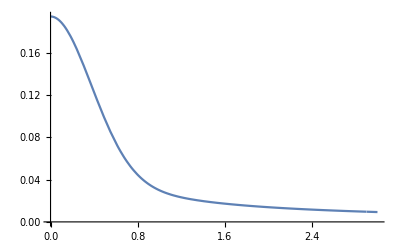

```mathematica
Plot[fvR1CaCl[r],{r,0,3}]
```

```mathematica
(*now calculate vtildeR1CaCl, I will use fvtR1CaCl to denote it.*)
```

```mathematica
fomegaCaCl[r_]:=NIntegrate[2 π rp^2(frhoqCa[rp])Qcl fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, rqcut},{x,-1,1}]+
1/2 NIntegrate[2 π rp^2(-Qcashield frhoqcorrect[rp])Qcl fvR1ClA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, 20},{x,-1,1}]+
NIntegrate[(Qcashield-Qcacut)/2 Qcl fvR1ClA[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}]+NIntegrate[2 π rp^2(frhoqCl[rp])Qca fvR1CaA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01, rqcut},{x,-1,1}]+
1/2 NIntegrate[2 π rp^2(-Qclshield frhoqcorrect[rp])Qca fvR1CaA[Sqrt[rp^2+r^2-2 r rp x]],{rp, 0.01,20},{x,-1,1}]+
NIntegrate[(Qclshield-Qclcut)/2 Qca fvR1CaA[Sqrt[rqcut^2+r^2-2 r rqcut x]],{x,-1,1}]
```

```mathematica
tableomegaCaCl=ParallelTable[fomegaCaCl[r],{r,0.005,4,0.05}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0267899 and 3.62247×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.118244 and 2.79148×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0531483 and 5.41905×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0280669 and 7.77641×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.142691 and 1.11434×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0593177 and 6.07786×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0250998 and 3.47731×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.1074 and 5.55141×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0471711 and 3.96503×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.181529 and 1.89663×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.169733 and 3.04759×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.128854 and 2.24159×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0189922 and 2.44558×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0197517 and 5.18099×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.018334 and 3.00949×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0152932 and 1.38247×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0129119 and 2.08874×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0111779 and 3.95154×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0158077 and 2.89759×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0131294 and 1.48062×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0112266 and 6.02281×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0148936 and 1.24451×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0126348 and 6.11808×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0109631 and 2.71538×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00981166 and 1.58174×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00982243 and 3.19353×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0096409 and 1.43128×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00886638 and 9.72141×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00887354 and 1.87219×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00809175 and 1.08301×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00872592 and 8.86629×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00797465 and 1.00438×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00786089 and 9.86624×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.350903,0.347706,0.339359,0.326284,0.309132,0.28873,0.266006,0.241908,0.217364,0.193206,0.170129,0.148668,0.129189,0.111896,0.09685,0.0839917,0.0731794,0.0642048,0.0568346,0.0508266,0.0459462,0.0419793,0.0387398,0.0360702,0.0338419,0.0319533,0.0303253,0.0288982,0.0276272,0.0264794,0.0254307,0.0244639,0.0235659,0.0227275,0.0219415,0.0212023,0.0205057,0.019848,0.0192262,0.0186375,0.0180795,0.01755,0.017047,0.0165687,0.0161131,0.0156791,0.0152644,0.0148684,0.0144897,0.0141272,0.0137799,0.013447,0.0131277,0.0128212,0.012527,0.0122443,0.0119727,0.0117115,0.0114604,0.0112187,0.0109861,0.0107621,0.0105463,0.0103382,0.0101376,0.00994415,0.00975736,0.009577,0.00940276,0.00923436,0.00907153,0.00891401,0.00876158,0.00861401,0.00847108,0.0083326,0.00819837,0.00806822,0.00794198,0.00781948}

```mathematica
interpomegaCaCl=Interpolation[Transpose[{Table[r,{r,0.005,4,0.05}],tableomegaCaCl}]]
```

InterpolatingFunction[…]

```mathematica
fvtR1CaCl[r_]:=Piecewise[{{interpomegaCaCl[r]/(Qca Qcl)+fvR1CaCl[r], r<3.9}, {1/(ϵ r), r>=3.9}}]
```

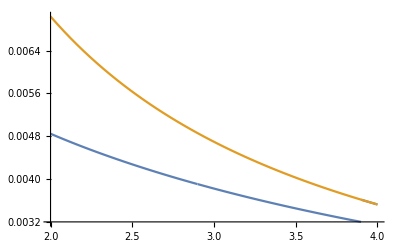

```mathematica
Plot[{fvtR1CaCl[r],1/(ϵ r)},{r,2,4},PlotRange->Full]
```

```mathematica
tableomegaCaCllong=ParallelTable[fomegaCaCl[r],{r,0.005,10,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0600685 and 3.74052×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0138248 and 9.08821×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0205229 and 3.09927×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0679219 and 6.35415×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0141644 and 1.82452×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0213502 and 6.00247×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0531483 and 5.41905×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0135055 and 7.98157×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0197166 and 2.5872×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.181529 and 1.89663×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.169733 and 3.04759×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.128854 and 2.24159×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0105539 and 7.64652×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0105772 and 1.161×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0103591 and 2.035×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00846464 and 1.43896×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00833658 and 1.30031×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00821234 and 1.43002×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.350903,0.347706,0.339359,0.326284,0.309132,0.28873,0.266006,0.241908,0.217364,0.193206,0.170129,0.148668,0.129189,0.111896,0.09685,0.0839917,0.0731794,0.0642048,0.0568346,0.0508266,0.0459462,0.0419793,0.0387398,0.0360702,0.0338419,0.0319533,0.0303253,0.0288982,0.0276272,0.0264794,0.0254307,0.0244639,0.0235659,0.0227275,0.0219415,0.0212023,0.0205057,0.019848,0.0192262,0.0186375,0.0180795,0.01755,0.017047,0.0165687,0.0161131,0.0156791,0.0152644,0.0148684,0.0144897,0.0141272,0.0137799,0.013447,0.0131277,0.0128212,0.012527,0.0122443,0.0119727,0.0117115,0.0114604,0.0112187,0.0109861,0.0107621,0.0105463,0.0103382,0.0101376,0.00994415,0.00975736,0.009577,0.00940276,0.00923436,0.00907153,0.00891401,0.00876158,0.00861401,0.00847108,0.0083326,0.00819837,0.00806822,0.00794198,0.00781948,0.00770057,0.00758512,0.00747297,0.00736401,0.0072581,0.00715513,0.00705499,0.00695756,0.00686275,0.00677046,0.0066806,0.00659307,0.0065078,0.0064247,0.0063437,0.00626472,0.0061877,0.00611256,0.00603924,0.00596769,0.00589783,0.00582961,0.00576299,0.0056979,0.0056343,0.00557214,0.00551137,0.00545195,0.00539384,0.00533699,0.00528138,0.00522695,0.00517367,0.00512151,0.00507044,0.00502042,0.00497142,0.00492341,0.00487636,0.00483025,0.00478505,0.00474072,0.00469726,0.00465463,0.0046128,0.00457177,0.0045315,0.00449197,0.00445317,0.00441508,0.00437767,0.00434093,0.00430484,0.00426938,0.00423454,0.0042003,0.00416665,0.00413357,0.00410104,0.00406906,0.0040376,0.00400666,0.00397623,0.00394628,0.00391681,0.00388781,0.00385927,0.00383117,0.00380351,0.00377627,0.00374944,0.00372302,0.003697,0.00367136,0.0036461,0.00362121,0.00359668,0.0035725,0.00354867,0.00352517,0.00350201,0.00347917,0.00345664,0.00343443,0.00341251,0.0033909,0.00336957,0.00334853,0.00332776,0.00330727,0.00328704,0.00326708,0.00324737,0.00322792,0.0032087,0.00318973,0.003171,0.0031525,0.00313422,0.00311617,0.00309834,0.00308072,0.00306331,0.00304611,0.00302911,0.00301231,0.00299571,0.00297929,0.00296307,0.00294703,0.00293117,0.00291549,0.00289998,0.00288464,0.00286948,0.00285448,0.00283964,0.00282497,0.00281045,0.00279608}

```mathematica
interpomegaCaCllong=Interpolation[Transpose[{Table[r,{r,0.005,10,0.05}],tableomegaCaCllong}]]
```

InterpolatingFunction[…]

```mathematica
fvtR1CaCllong[r_]:=Piecewise[{{interpomegaCaCllong[r]/(Qca Qcl)+fvR1CaCl[r], r<9.9}, {1/(ϵ r), r≥9.9}}]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

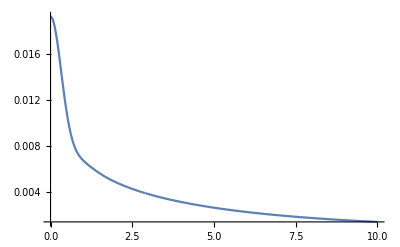

```mathematica
Plot[{fvtR1CaCllong[r]},{r,0,10},PlotRange->Full]
```

```mathematica
Export["vR1_CaCl.txt", Transpose[{Table[r,{r,0.02,20,0.02}], Table[fvtR1CaCllong[r],{r,0.02,20,0.02}]}], "Table"]
```

```mathematica
fvtR1CaCllong[0.2]
```

0.0171579

```mathematica
box=2.97
```

2.97

```mathematica
fvtR1CaCllongs[r_]:=fvtR1CaCllong[r]-Erf[r/10]/(ϵ r)
```

```mathematica
fEwaldCaCl[x_]:=Sum[Qca Qcl fvtR1CaCllongs[Sqrt[(m box-x)^2+(l box)^2+(n box)^2]],{m,-20,20},{l,-20,20},{n,-20,20}]
```

```mathematica
tableEwaldCaCl=ParallelTable[fEwaldCaCl[r],{r,0.1,1.5,0.05}]
```

{-0.321209,-0.319895,-0.318236,-0.316233,-0.314057,-0.311829,-0.309653,-0.307612,-0.305769,-0.304187,-0.302826,-0.301707,-0.300808,-0.300076,-0.299528,-0.299107,-0.298783,-0.29853,-0.29831,-0.298146,-0.298011,-0.297896,-0.2978,-0.29772,-0.297655,-0.297633,-0.297599,-0.297632,-0.297629}

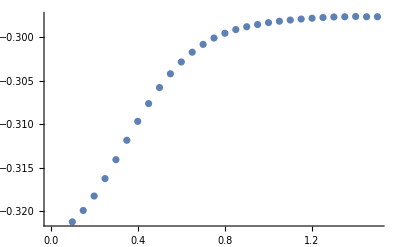

```mathematica
ListPlot[Transpose[{Table[r,{r,0.1,1.5,0.05}], tableEwaldCaCl}]]
```

```mathematica
interpEwaldCaCl=Interpolation[Transpose[{Table[r,{r,0.1,1.5,0.05}], tableEwaldCaCl}]]
```

InterpolatingFunction[…]

```mathematica
Export["VR1CaCl_Ewald.txt",Transpose[{Table[r,{r,0.1,box/2,0.001}], Table[interpEwaldCaCl[r]-interpEwaldCaCl[box/2],{r,0.1,box/2,0.001}]}],"Table"]
```

```mathematica
140*(interpEwaldCaCl[0.3]-interpEwaldCaCl[box/2])
```

-2.29837